https://www.alternatewars.com/BBOW/Ballistics/Term/AP/AP_Pen_Formula.htm

NAVY 1940s “Universal” Formula

W=Weight of Shell (grams)
D=Diameter of Shell (millimeters)
V=Striking Velocity of Shell (m/second)

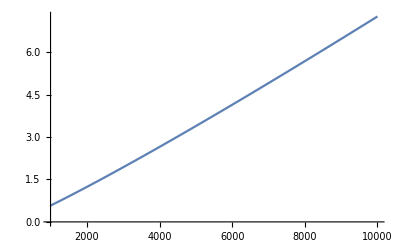

```mathematica
ClearAll[w,d,v,f,g]
f[w_,d_,v_]:=(0.000469)*w^0.5506*d^-0.6521*v^1.1001
g[w_,d_,v_]:=f[w/454,25.4/d,v/0.305]*25.4
Plot[g[1,2,v],{v,1000,10000}]
```

ARMY 1982 Lambert-Zukas (V50) Penetration Formula

T = Armor Plate Thickness (cm)
θ = Angle of Impact (radians)
D = Projectile Diameter (cm)

VL = Limit Velocity (m/sec) for 50/50 penetration
α = Armor Constant (4,000 for RHA; 1,750 for 2.77 g/cc Aluminum).
L = Projectile Length (cm)
D = Projectile Diameter (cm)
Z = Z Factor (calculated previously, dimensionless)
M = Projectile Mass (grams)

```mathematica
Solve[
{vl==a*(l/d)^0.15*√(((z+E^-z-1)*d^3)/M )  ,  z==(t*1^0.75)/d},
t]
```

The Original F-Formula (as given by Nathan Okun)


t=Armor Thickness (milimeters)
d=Projectile Diameter (milimeters)
m=Projectile Mass (grams)
vl=Impact velocity that projectile must have to reach ballistic limit for the plate (m/sec).

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

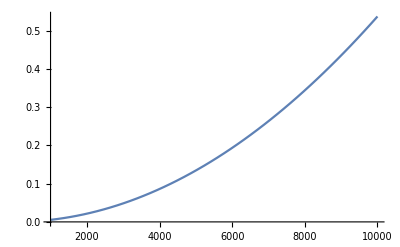

```mathematica
ClearAll[f,g,fstd,vl,t,d,θ,res,m]
θ=0;
res=Solve[Reduce[Eliminate[
{fstd==6*(t/d-0.45)*(θ^2+2000)+40000,
vl==(1/41.57)*fstd*√(t/d)*√((d)^3/m)*1/Cos[θ]},fstd
]  && Element[vl,PositiveReals]   && Element[m,PositiveReals]  && Element[d,PositiveReals]  && Element[t,PositiveReals]   ],t,PositiveReals]//Values;
f[m_,d_,vl_]:=res[[1,1,1]]//Evaluate
g[m_,d_,vl_]:=f[m/454,25.4/d,vl/0.305]*25.4

Plot[g[1,2,x],{x,1000,10000}]
```

```mathematica
Root[-5.35956162042015*^14 m vl^2+3.7129698019456254*^20 d^2 #1+2.5754703828524568*^20 d #1^2+4.466133611882873*^19 #1^3&,1]
```

Root[-5.35956×10^14 m vl^2+3.71297×10^20 d^2 #1+2.57547×10^20 d #1^2+4.46613×10^19 #1^3&,1]

```mathematica
FullSimplify[-5.35956162042015*^14 (454m) *(0.305)^2+3.7129698019456254*^20 d^2 #1+2.5754703828524568*^20 d #1^2+4.466133611882873*^19 #1^3&]
```

-5.35956×10^14 (454 m) 0.305^2+3.71297×10^20 d^2 #1+2.57547×10^20 d #1^2+4.46613×10^19 #1^3&